```mathematica
<<SpinWeightedSpheroidalHarmonics`
<<KerrGeodesics`
<<GeneralRelativityTensors`
<<Teukolsky`
ParallelNeeds["SpinWeightedSPheroidalHarmonics`"]
ParallelNeeds["KerrGeodesics`"]
ParallelNeeds["GeneralRelativityTensors`"]
ParallelNeeds["Teukolsky`"]
```

```mathematica
prec=32;
```

```mathematica
𝔰[sp_,l_,lp_, m_]:= -sp  Sqrt[(2(2l+1))/(2 lp +1)]ClebschGordan[{l,m},{1,0},{lp,m}] ClebschGordan[{l,-sp} ,{1,sp }, {lp ,0}]
Ccoef[s_,j_,k_,m_,bs_]:=𝔰[s,j,k,m]*(j/.bs);
CLcoef [a_,m_,n_,j_,k_,ω_, bs_]:=(j/.bs)*(Sqrt[j(j+1)] KroneckerDelta[j,k] - a ω 𝔰[+1, j,k,m]);
```

```mathematica
Fr0[a_,τ_,  orbit_, k_,m_,n_, LMAX_, JMAX_]:= Module[{t, r,θ,φ, tdot, phidot,  rmin, rmax},
{t,r,θ,φ}=orbit["Trajectory"];
rmin = orbit["p"]/(1+orbit["e"]+0.1);
     rmax = orbit["p"]/(1-orbit["e"]-0.1);
Sum[Module[{bsplus,bsminus,χ, g, dP, K0,Β,Pminus, Pplus,Rminus,  Δ, λ},
λ = SpinWeightedSpheroidalEigenvalue[-1,l,m,a ω[m,n]];
Β= Sqrt[λ^2+ 4 a m ω[m,n] - 4 a^2 ω[m,n]^2];
K0= ω[m,n]((r[τ])^2 + a^2)- a m;
bsplus = SpinWeightedSpheroidalHarmonicS[1,l,m,a ω[m,n],Method->{"SphericalExpansion","NumTerms"->6}]["ExpansionCoefficients"] ;
bsminus = SpinWeightedSpheroidalHarmonicS[-1,l,m,a ω[m,n],Method->{"SphericalExpansion","NumTerms"->6}]["ExpansionCoefficients"] ;
Rminus=TeukolskyRadial[-1, l,m,a ,ω[m,n],Method->{"NumericalIntegration","Domain"-> {"In"->{rmin,rmax}, "Up"->{rmin,rmax}}}];
Pminus= Rminus["In"][r[τ]];
Δ=r[τ]^2-2 M r[τ] + a^2/.M->1;
Pplus = Δ TeukolskyRadial[1,l,m,a,ω[m,n], Method->{"NumericalIntegration","Domain"-> {"In"->{rmin,rmax}, "Up"->{rmin,rmax}}}]["Up"][r[τ]];
dP =Rminus["In"]'[r[τ]];

g= 1/Β (r[τ] dP- ⅈ K0 r[τ]/Δ Pminus-Pminus);
χ=Exp[-ⅈ ω[m,n] t[τ] + ⅈ m φ[τ]];
(Sqrt[2] (t'[τ] - a φ'[τ]))/r[τ]^2 Re[χ(CLcoef[a, m, n ,j,k,ω[m,n],bsplus]g + ⅈ a Ccoef[1, j, k, m , bsplus]/Β)] + (φ'[τ] *(a^2+r[τ]^2) + a t'[τ])/(Sqrt[2] Δ r[τ])Im[
χ(Ccoef[-1, j,k,m, bsminus]TeukolskyPointParticleMode[-1,l,m,n,0, orbit] ["ExtendedHomogeneous" -> "ℋ"][r[τ]]Pminus - Ccoef[1,j,k,m, bsplus] TeukolskyPointParticleMode[1,l,m,n,0, orbit] ["ExtendedHomogeneous" -> "ℋ"][r[τ]] Pplus)]

],{l,Max[1,Abs[m]],LMAX}, {j, Max[1, Abs[m]], JMAX}]
]
```

```mathematica
ParallelEvaluate[Off[ClebschGordan::tri ]]
ParallelEvaluate[Off[ClebschGordan::phy]]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
With[{a=SetPrecision[0,prec], e=SetPrecision[0.1,prec],p=SetPrecision[10,prec],x=1, τ=0.5,NMax=3},
q=1;
orbit = KerrGeoOrbit[a,p,e,x]; 
Ω =KerrGeoFrequencies[a,p,e,x];
ω[m_,n_]:=m Ω[[3]] + n Ω[[1]];
kmodes = Table[
ParallelSum[Fr0[a,τ,  orbit,k ,m,n, NMax, NMax], {m,-NMax,NMax}, {n,-NMax, NMax}],{k,1,5}]
]
```

TeukolskyRadial::sopt: Option Method not supported for static (ω=0) modes.

General::stop: Further output of TeukolskyRadial::sopt will be suppressed during this calculation.

TeukolskyRadial::sopt: Option Method not supported for static (ω=0) modes.

General::stop: Further output of TeukolskyRadial::sopt will be suppressed during this calculation.

TeukolskyRadial::sopt: Option Method not supported for static (ω=0) modes.

General::stop: Further output of TeukolskyRadial::sopt will be suppressed during this calculation.

TeukolskyRadial::sopt: Option Method not supported for static (ω=0) modes.

General::stop: Further output of TeukolskyRadial::sopt will be suppressed during this calculation.

TeukolskyRadial::sopt: Option Method not supported for static (ω=0) modes.

General::stop: Further output of TeukolskyRadial::sopt will be suppressed during this calculation.

{-343.952,-4541.21,-56171.8,-442.047,0.}

```mathematica
R["Up"][20]
```

0.000146275+0. ⅈ

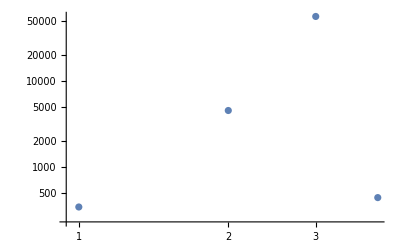

```mathematica
ListLogLogPlot[{Abs[kmodes]}]
```

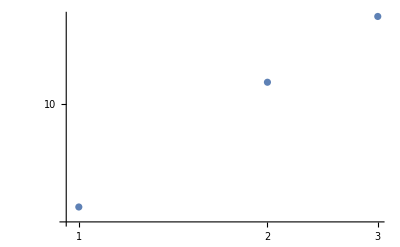

```mathematica
ListLogLogPlot[Table[{k,Log[kmodes[[k]]]}, {k,1,3}]]
```

```mathematica
PlotOrbit[orbit_]=Module[{t, r, θ, φ},
{t, r, θ,φ} = orbit["Trajectory"];

Show[ParametricPlot3D[{r[λ] Sin[θ[λ]] Cos[φ[λ]],r[λ] Sin[θ[λ]] Sin[φ[λ]],r[λ] Cos[θ[λ]]},{λ,0,20},Boxed->False,Axes->False,PlotStyle->Red,PlotRange->All],Graphics3D[{Black,Sphere[{0,0,0},1+Sqrt[1-orbit["a"]^2]]}]]
]
```

-Graphics3D-

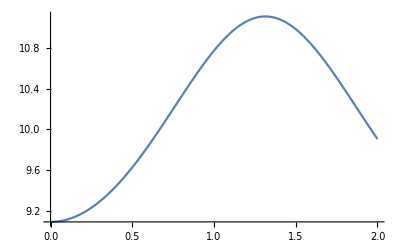

```mathematica
Module[{t, r, θ,φ},{t,r,θ, φ} = orbit["Trajectory"];
Plot[r[τ],{τ,0,2}]
]
```